# Angles Gram Matrix and Tetrahedron Reconstruction

## Angles Gram Matrix and definitions

### Definition of Gram Matrix

The Angles Gram matrix encodes the geometry of a tetrahedron by relating its face normals. When expressed in terms of the external dihedral angles ϕ_ab between the faces a and b, its entries are given by G_ab = cos(ϕ_ab), with the diagonal elements set to 1.

```mathematica
Gram = ({{1, Cos[ph12], Cos[ph13], Cos[ph14]}, {Cos[ph12], 1, Cos[ph23], Cos[ph24]}, {Cos[ph13], Cos[ph23], 1, Cos[ph34]}, {Cos[ph14], Cos[ph24], Cos[ph34], 1}});
```

This matrix is symmetric and real, and its determinant imposes a necessary condition for the angles to correspond to a Euclidean tetrahedron: the vanishing of det(G) indicates that the four face normals close to form a three-dimensional object. Studying the Gram matrix thus allows us to characterize whether a set of external angles defines an admissible classical tetrahedron or not.

Of course the det(G)=0  is a constraint on the angles, telling us that we cannot choose all 6 of them freely. We will call this the closure constraint. We define as an example the substitution corresponding to the regular tetrahedron

```mathematica
regular = {ph12->ArcCos[-1/3], ph13->ArcCos[-1/3], ph14->ArcCos[-1/3],ph23->ArcCos[-1/3],ph24->ArcCos[-1/3],ph34 ->ArcCos[-1/3]};
```

```mathematica
GramRegular= Gram/.regular
```

{{1,-1/3,-1/3,-1/3},{-1/3,1,-1/3,-1/3},{-1/3,-1/3,1,-1/3},{-1/3,-1/3,-1/3,1}}

```mathematica
Det[GramRegular]
```

0

### Areas and Kernel

The kernel, or the null space of the Gram matrix is proportional to the area vector — the vector containing the areas of the tetrahedron’s faces. This follows directly from the closure condition of the face normals. Note that the scale of the tetrahedron is not encoded in the Gram matrix, as it is scale-invariant, so the overall size cannot be determined. Since Mathematica conventionally sets the first entry of the null space vector to 1, we will compute the other areas as fractions of the first one.

```mathematica
Areas[subs_]:=NullSpace[Gram/.subs]
```

```mathematica
Areas[regular]
```

{{1,1,1,1}}

Which is compatible with all areas being the same in the regular tetrahedron.

### Definition of M Matrix

The M matrix defined in the paper plays a crucial role in the reality condition for the volume as well as the edge lengths. Its entries are M_ab= sin^2(ϕ_ab) with diagonal elements set to zero.

```mathematica
M = ({{0, Sin[ph12]^2, Sin[ph13]^2, Sin[ph14]^2}, {Sin[ph12]^2, 0, Sin[ph23]^2, Sin[ph24]^2}, {Sin[ph13]^2, Sin[ph23]^2, 0, Sin[ph34]^2}, {Sin[ph14]^2, Sin[ph24]^2, Sin[ph34]^2, 0}});
```

The determinant of the M matrix enters into the formula for the lengths. Note that M is also scale invariant, and thus the lengths are still fixed only up-to an arbitrary scale.

### Lengths and derivatives

The edge lengths of the tetrahedron can, in principle, be extracted from the derivatives of the determinant of the Gram matrix with respect to the external angles. However, as with the areas, the Gram matrix does not encode the overall scale of the tetrahedron, which remains undetermined. Since the scale of the lengths is different from that of the areas, and we are not interested in fixing it here, the two will not be compatible in general. To make them compatible we should scale one of the two appropriately.

```mathematica
Lengths[phi_]:=-4/(√(- Det[M]))D[Det[Gram],phi]
```

```mathematica
{Lengths[ph12],Lengths[ph13],Lengths[ph14],Lengths[ph23],Lengths[ph24],Lengths[ph34]}/.regular
```

{4 √(2/3),4 √(2/3),4 √(2/3),4 √(2/3),4 √(2/3),4 √(2/3)}

Which is compatible with all lengths being the same in the regular tetrahedron.

```mathematica
AllLengths[sub_]:={Lengths[ph12],Lengths[ph13],Lengths[ph14],Lengths[ph23],Lengths[ph24],Lengths[ph34]}/.sub
```

### Drawing the tetrahedron

```mathematica
ReconstructTet[sub_]:=Module[{v1,v2,v3,v4,x3,y3,x4,y4,z4,l12,l13,l14,l23,l24,l34},
l12=Lengths[ph12]/.sub;
l13=Lengths[ph13]/.sub;
l14=Lengths[ph14]/.sub;
l23=Lengths[ph23]/.sub;
l24=Lengths[ph24]/.sub;
l34=Lengths[ph34]/.sub;
v1={0,0,0};
v2={l12,0,0};
x3=(l12^2+l13^2-l23^2)/(2 l12);
y3=√(l13^2-x3^2);
v3={x3,y3,0};
x4=(l12^2+l14^2-l24^2)/(2 l12);
y4=(-l12^2+l24^2-l34^2+x3^2+2 l12 x4-2 x3 x4+y3^2)/(2 y3);
z4=√(l14^2-x4^2-y4^2);
v4={x4,y4,z4};
Tetrahedron[{v1,v2,v3,v4}]
]
```

```mathematica
Graphics3D[{Opacity[0.8],EdgeForm[Black],ReconstructTet[regular]},Boxed->False]
```

-Graphics3D-

## Symmetric tetrahedron

Studying the fully generic case is too complicated. Therefore, we fix ϕ_14, set ϕ_12 equal to ϕ_34, and set ϕ_13 equal to ϕ_24, and finally choosing ϕ_23 in such a way we satisfy the det(G)=0 constraint. This choice may seem arbitrary, but it is made so that the four face areas are grouped into two pairs of equal areas.

```mathematica
symmetry = {ph12->ph34,ph13->ph24,ph14 ->ArcCos[-1/3]};
```

We choose the value of ϕ_14 to be equal to ArcCos[-1/3] to connect with the regular tetrahedron.

```mathematica
GramSym=Gram/.symmetry;
GramSym //MatrixForm
```

(1 | Cos[ph34] | Cos[ph24] | -1/3
Cos[ph34] | 1 | Cos[ph23] | Cos[ph24]
Cos[ph24] | Cos[ph23] | 1 | Cos[ph34]
-1/3 | Cos[ph24] | Cos[ph34] | 1)

### Imposing the closure constraint

To fix ϕ_23, we impose the condition det(G)=0, which can be solved directly in terms of Cos(ϕ_23).

```mathematica
{sol1,sol2}=Solve[Det[GramSym/.Cos[ph23]->C23]==0,C23]
```

{{C23→1/8 (2-3 Cos[2 ph24]+6 Cos[ph24-ph34]-3 Cos[2 ph34]+6 Cos[ph24+ph34])},{C23→1/4 (2+3 Cos[2 ph24]+6 Cos[ph24-ph34]+3 Cos[2 ph34]+6 Cos[ph24+ph34])}}

We specify the Gram matrix on-shell of these two solutions. We will decide later on which solution we want to focus.

```mathematica
GramSym1=GramSym/.Cos[ph23]->Last@Last[sol1];
GramSym2=GramSym/.Cos[ph23]->Last@Last[sol2];
```

Test if the Closure Constraint is satisfied in both solutions

```mathematica
{Det[GramSym1],Det[GramSym2]}//FullSimplify
```

{0,0}

### Drawing the tetrahedron

Let’s draw an example by using the second solution to ϕ_23 that we obtain from the closure condition, i.e. sol2.

```mathematica
SymmetricExample[choice_] :=Module[{s1,s2,s3},
s1 = symmetry/.choice;
s2 = {ph23->ArcCos[Last@Last[sol2]/.choice]};
s3= choice;
Join[s1,s2,s3]
];
```

```mathematica
symmetrictest = SymmetricExample[{ph34-> ArcCos[-1/3],ph24->ArcCos[-1/3]+0.3}];
```

We can find all the lengths (upto a scale)

```mathematica
AllLengths[symmetrictest]//N
```

{2.82908,2.40713,3.94825,2.05211,2.40713,2.82908}

We can find all the Areas (upto a scale different to that of length of course)

```mathematica
Areas[symmetrictest]//FullSimplify
```

{{0.574783,0.411855,0.411855,0.574783}}

The signature of the Gram matrix is euclidean (3,0,1)

```mathematica
Chop[Eigenvalues[Gram/.symmetrictest]//N]
```

{1.96513,1.42895,0.605921,0}

```mathematica
Graphics3D[{Opacity[0.8],EdgeForm[Black],ReconstructTet[symmetrictest]},Boxed->False]
```

-Graphics3D-

### Non-realizable geometric configurations

However, notice that for this solution, there are a few choices which are not “realizable” tetrahedra -

```mathematica
negareastest = SymmetricExample[{ph34-> 1.4,ph24->1.6}];
```

```mathematica
Areas[negareastest]
```

{{-0.146086,0.691852,0.691852,-0.146086}}

```mathematica
AllLengths[negareastest]
```

{-3.2399,-3.28634,0.654508,3.76804,-3.28634,-3.2399}

### Lorentzian configurations

You can also find non embeddable positive areas tetrahedra - These correspond to Lorentzian tetrahedra.

```mathematica
lorentzian = SymmetricExample[{ph34->3,ph24->1.5}];
```

```mathematica
Areas[lorentzian]//N
```

{{0.57242,0.415133,0.415133,0.57242}}

As mentioned earlier, the reality of the length of the edges depend on the sign of the determinant of the M Matrix. In the Lorentzian case, we have

```mathematica
Sqrt[-Det[M]]/.lorentzian
```

0.+0.160327 ⅈ

```mathematica
AllLengths[lorentzian]//N
```

{0.+0.480757 ⅈ,0.+3.39819 ⅈ,0.+4.42882 ⅈ,0.+2.38057 ⅈ,0.+3.39819 ⅈ,0.+0.480757 ⅈ}

The signature of the Gram matrix in this example is Minkowskian (2,1,1)

```mathematica
Chop[Eigenvalues[Gram/.lorentzian]//N]
```

{2.13535,1.93421,-0.069563,0}

We can also obtain solutions to the Closure constraint that involve analytically continued values for ϕ_23. For example,

```mathematica
lorentzian2 = SymmetricExample[{ph34->3,ph24->3}];
```

```mathematica
ArcCos[Last@Last@sol2]/.lorentzian2//N
```

0.+2.26773 ⅈ

But, notice that in this scenario the length  (l_23) corresponding to the imaginary angle (ϕ_23) is real - thus, their product in the Regge action remains imaginary.

```mathematica
AllLengths[lorentzian2] //N
```

{0.+0.285082 ⅈ,0.+0.285082 ⅈ,0.+5.65663 ⅈ,-3.24923+0. ⅈ,0.+0.285082 ⅈ,0.+0.285082 ⅈ}

At first glance this looks wrong. Since we find a negative length. However this is a consequence of picking the wrong branch for the ArcCos function. If we choose the negative branch (-ArcCos) one we find

```mathematica
SymmetricExampleCorrectBranch[choice_] :=Module[{s1,s2,s3},
s1 = symmetry/.choice;
s2 = {ph23->-ArcCos[Last@Last[sol2]/.choice]};
s3= choice;
Join[s1,s2,s3]
];
```

```mathematica
lorentzian2CorrectBranch = SymmetricExampleCorrectBranch[{ph34->3,ph24->3}];
```

```mathematica
-ArcCos[Last@Last@sol2]/.lorentzian2CorrectBranch//N
```

0.-2.26773 ⅈ

The real length is positive

```mathematica
AllLengths[lorentzian2CorrectBranch] //N
```

{0.+0.285082 ⅈ,0.+0.285082 ⅈ,0.+5.65663 ⅈ,3.24923+0. ⅈ,0.+0.285082 ⅈ,0.+0.285082 ⅈ}

These configurations still have a positive null eigenspace, and they still correspond to tetrahedron with Lorentzian signature (2,1,1).

```mathematica
Areas[lorentzian2]//N
```

{{1.,0.336703,0.336703,1.}}

```mathematica
Chop[Eigenvalues[Gram/.lorentzian2]//N]
```

{6.54718,-3.88051,1.33333,0}

## Exploring the space of symmetric tetrahedra

Now, let us look at the entire configuration space of boundary surfaces spanned by the two unfixed angles - ϕ_24 and ϕ_34 - they vary between 0 and π. 
We can differentiate between Euclidean and Lorentzian geometries by checking the signature of the corresponding gram matrix G_ab.

### All Geometric Configurations

In the Graph below, the blue region correspond to geometric configurations such that their corresponding Gram Matrix has Euclidean (3,0,1) signature. Similarly, the white regions correspond to Lorentzian configurations with (2,1,1) Gram Matrix signature.

```mathematica
countNegatives[G_]:=Module[{vals,filtered},vals=Eigenvalues[G];
filtered=Select[vals,Abs[#]>10^-10&];
Count[filtered,_?Negative]]
```

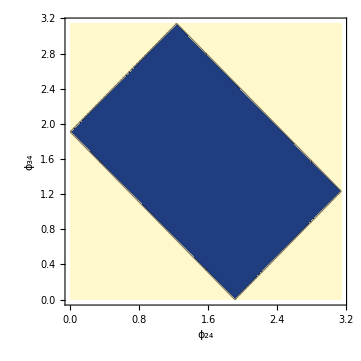

```mathematica
plot=ContourPlot[countNegatives[GramSym2],{ph24,0,Pi},{ph34,0,Pi},Contours->1,WorkingPrecision->20,PlotPoints->100,FrameLabel->{Subscript[ϕ, 24],Subscript[ϕ, 34]}]
```

### Possible Tetrahedral configurations

We can figure out which of these geometric configurations correspond to admissible tetrahedra - for such configurations (both Euclidean and Lorentzian), the null space or the Area vector has to be a positive vector. 
The Area vector for the symmetric configuration is given by

```mathematica
Areas[SymmetricExample[{ph34-> Subscript[ϕ, 34],ph24->Subscript[ϕ, 24]}]]//FullSimplify
```

{{1,-2/(3 (Cos[ϕ_24]+Cos[ϕ_34])),-2/(3 (Cos[ϕ_24]+Cos[ϕ_34])),1}}

To have all positive areas you need to satisfy the following conditions

```mathematica
Reduce[0<Subscript[ϕ, 34]<π&&0<Subscript[ϕ, 24]<π    &&    Cos[Subscript[ϕ, 34]]+Cos[Subscript[ϕ, 24]]<0]//FullSimplify
```

0<ϕ_24<π&&ArcCos[-Cos[ϕ_24]]<ϕ_34<π

which corresponds to the region of the configuration space over the anti-diagonal, i.e.

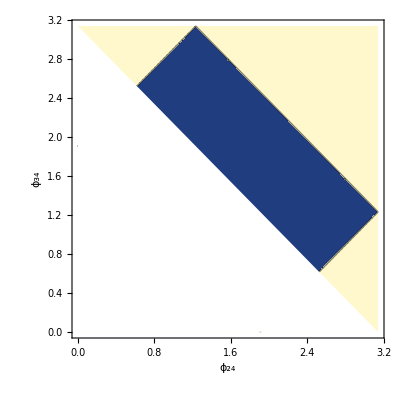

```mathematica
maskPolygon=Polygon[{{0,0},{Pi,0},{Pi,Pi-Pi},{0,Pi} }];
Show[plot,Graphics[{White,Opacity[1],maskPolygon}]]
```

In the Graph above, the blue region correspond to tetrahedral configurations with Euclidean (3,0,1) signature and the white region correspond to tetrahedral configurations with (2,1,1) Lorentzian signature.

### Configurations living on the boundary between Euclidean and Lorentzian tetrahedra

What about configurations that fall at the border between Euclidean and Lorentzian signatures? A hint as to what they correspond to can be obtained from their null space vector(s). 
The equation for the bottom right border is given by

```mathematica
cornertest = {ph24->ph24,ph34 ->ph24-ArcCos[-1/3]}
```

{ph24→ph24,ph34→ph24-ArcCos[-1/3]}

We see that the geometric configurations along this border have a corresponding Gram Matrix whose null eigen space is spanned by 2 vectors - thus the rank of the Gram Matrix is either (2,0,2) or (1,1,2) and they correspond to pencil like tetrahedron.

```mathematica
Areas[SymmetricExample[cornertest]]//FullSimplify
```

{{3-12/(4+√2 Tan[ph24]),8/(3 (-3 Cos[ph24]+Cos[ph24+ArcSec[3]])),0,1},{-(2 √2 Sin[2 ph24+ArcSec[3]])/(3 Cos[ph24]+Sin[ph24-ArcCsc[3]]),-3+12/(4+√2 Tan[ph24]),1,0}}

### Lorentzian configurations with imaginary dihedral angles and space-like edges.

Let us also study the configurations where the closure condition forces the angle ϕ_23 to attain a complex valued solution. The analytic continuation of ϕ_23 to purely complex values occurs through configurations where ϕ_23 attains zero value. Solving for that gives us the following equation

```mathematica
phi23zero = Cos[Last@Last@Solve[1==Last@Last@sol2,ph24][[2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/3 (-2 √3-3 Cos[ph34])

The points in the configurations space that have ϕ_23 = 0 correspond to the following ones (marked in Green). All tetrahedral configurations inside this arc have imaginary valued dihedral angle  ϕ_23. An example for such a configuration was shown in the previous section, where we also showed that the corresponding edge is space-like.
All the other configurations with Lorentzian signature and a positive null space correspond to Lorentzian tetrahedral configurations with real dihedral angles.

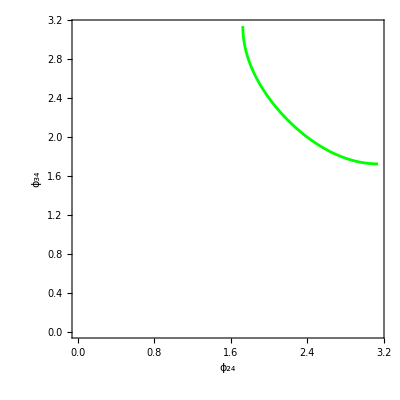

```mathematica
circle=ContourPlot[Cos[ph24]==phi23zero,{ph24,0,Pi},{ph34,0,Pi},Contours->1,WorkingPrecision->20,PlotPoints->100, ContourStyle->Green,FrameLabel->{Subscript[ϕ, 24],Subscript[ϕ, 34]}]
```

Putting all of them together, the following configurations correspond to either Euclidean or Lorentzian tetrahedral configurations. In the picture below, we also note the configuration that corresponds to a regular tetrahedron (red dot). We also demarcate the Lorentzian configurations with imaginary dihedral angles.

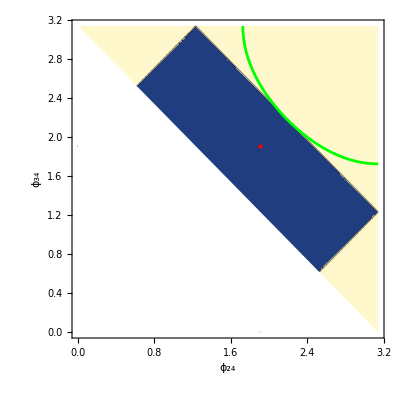

```mathematica
Show[plot,Graphics[{White,Opacity[1],maskPolygon}],Graphics[{Red,PointSize[Large],Point[{ArcCos[-1/3],ArcCos[-1/3]}]}],circle]
```